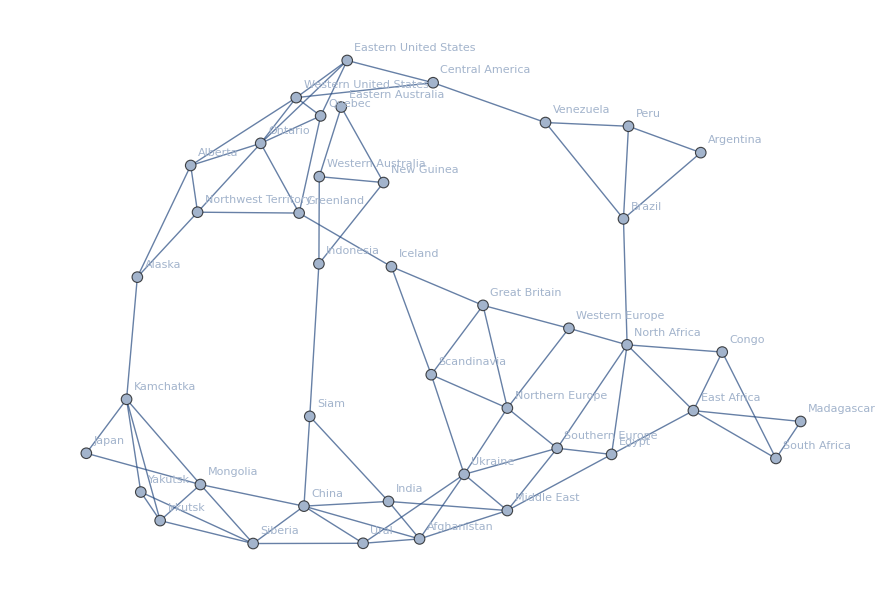

```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["SupportingFiles/RiskGameMap.txt","Table"];
Countries=Table[StringJoin[Riffle[data⟦i⟧," "]],{i,42}];
borders=Table[
line=data⟦i⟧;
Table[Countries⟦line⟦1⟧⟧<->Countries⟦line⟦j⟧⟧,{j,2,Length[line]}]

,{i,43,Length[data]}]//Flatten;
Graph[borders,VertexLabels->"Name",GraphLayout->"SpringEmbedding"]
```